```mathematica
Az=Integrate[Tanh[x],x]
```

Log[Cosh[x]]

```mathematica
By=Tanh[x]^3
Plot[By,{x,-2,2}]
Az=Integrate[-By,x]
Plot[Az,{x,-2,2}]
```

```mathematica
By=Tanh[x]
Plot[By,{x,-2,2}]
Az=Integrate[-By,x]
Plot[Az,{x,-2,2}]
```

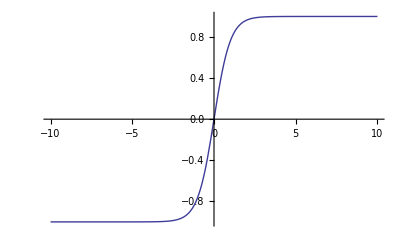

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

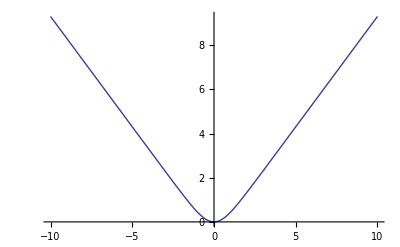

```mathematica
Plot[Az,{x,-10,10}]
```

1

0.1

-Log[Cosh[x]]+0.1 Log[Cosh[y]]

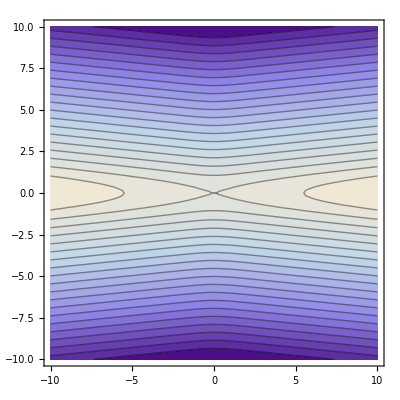

Log[Cosh[x]]

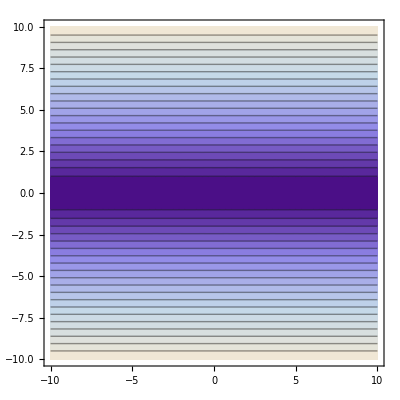

0.05 y^2-Log[Cosh[x]]

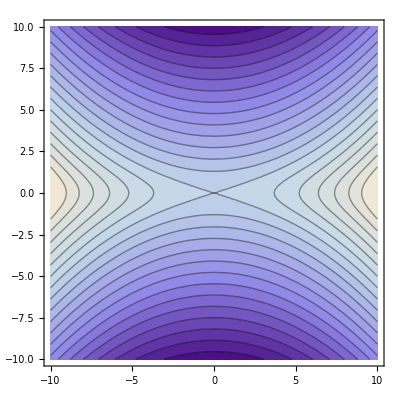

```mathematica
B0=1
B1=0.1
Az=-B0*Log[Cosh[x]]+B1*Log[Cosh[y]]
(*Az=B0*Log[Cosh[x]]+1*B0*Exp[-(x^2+y^2)/4]*)
ContourPlot[Az,{y,-10,10},{x,-10,10},Contours->20]
Az=B0*Log[Cosh[x]]
ContourPlot[Az,{y,-10,10},{x,-10,10},Contours->20]
Az=-B0*Log[Cosh[x]]+B1*y^2/2
ContourPlot[Az,{y,-10,10},{x,-10,10},Contours->20]
```

0.1

1

1

0.1

-5. x^2

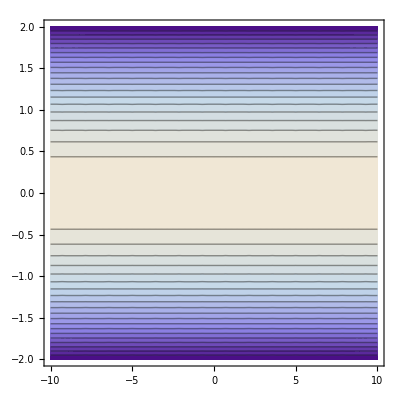

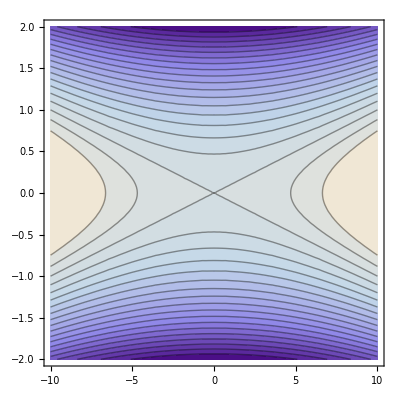

```mathematica
d=0.1
L=1
Byin=1
Bxout=0.1
Az=-Byin*(x/2)*(x/d)
ContourPlot[Az,{y,-10,10},{x,-2,2},Contours->20]
Az=-Byin*(x/2)*(x/d)+Bxout*(y/2)*(y/L);
ContourPlot[Az,{y,-10,10},{x,-2,2},Contours->20]
```

```mathematica
Clear[AA,BB,d,L,Byin,Bxout]
fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]
eq1=Byin==(fun//.{x->d,y->0})
eq2=Bxout==(fun//.{x->0,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
Az=fun//.solsfun[[1]]
```

AA Log[Cosh[x/d]]+BB Log[Cosh[y/L]]

Byin==AA Log[Cosh[1]]

Bxout==BB Log[Cosh[1]]

{{AA→Byin/Log[Cosh[1]],BB→Bxout/Log[Cosh[1]]}}

(Byin Log[Cosh[x/d]])/Log[Cosh[1]]+(Bxout Log[Cosh[y/L]])/Log[Cosh[1]]

```mathematica
(* GET A_z *)
```

{d→0.1,L→1,Byin→1,Bxout→0.1,Bxcorner→0.1,Bycorner→1}

{{CC→1/3 (Bycorner d-Byin d+2 Bxcorner L-2 Bxout L),DD→1/3 (-2 Bycorner d+2 Byin d-Bxcorner L+Bxout L),AA→-(Byin d)/2,BB→(Bxout L)/2}}

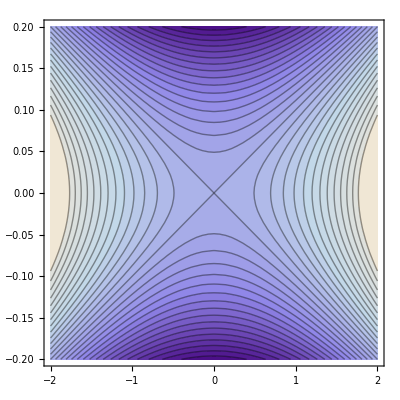

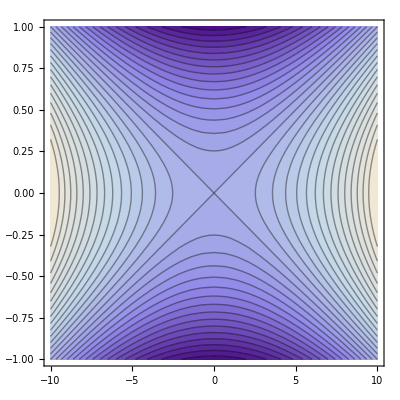

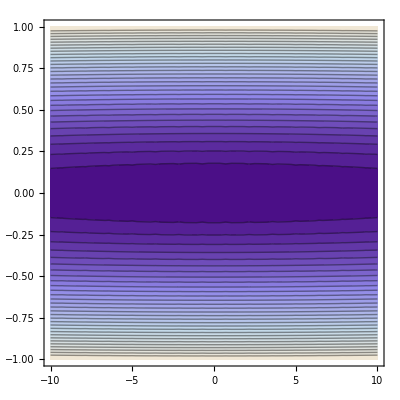

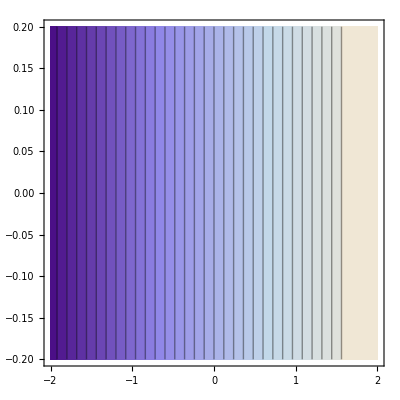

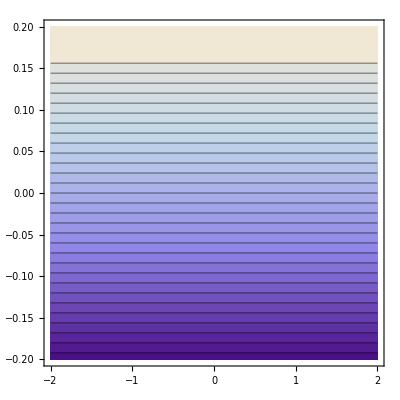

cosh version2

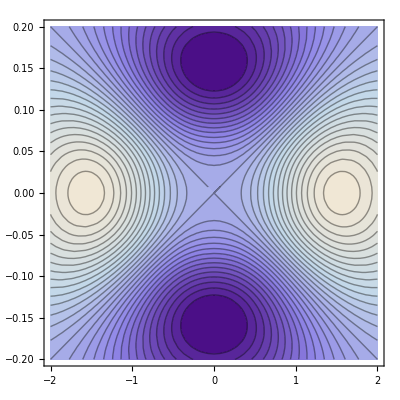

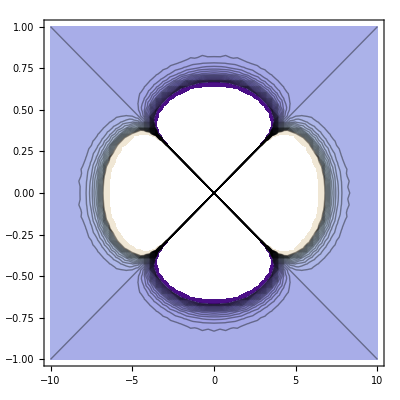

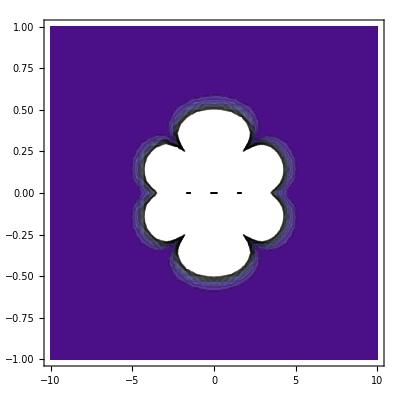

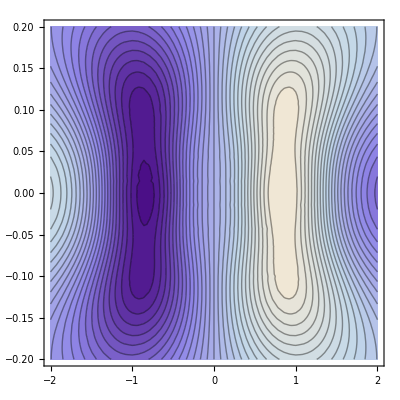

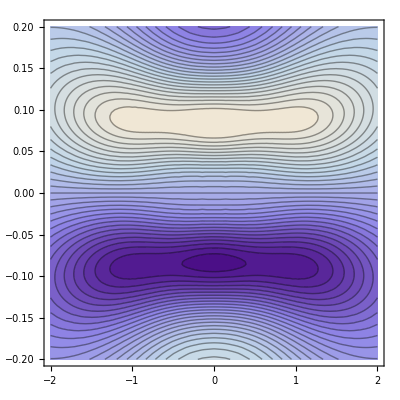

cosh version3

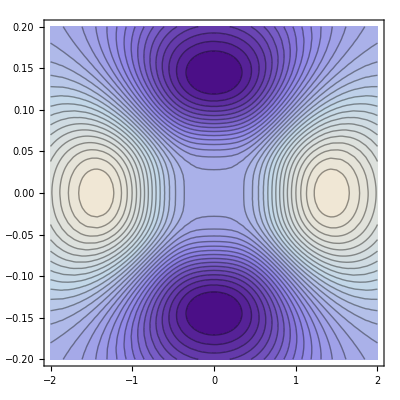

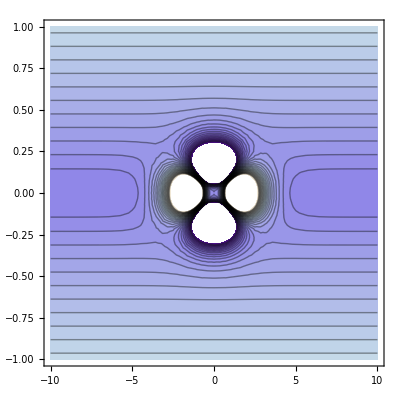

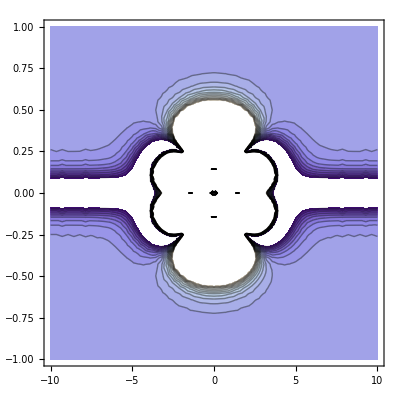

-Graphics-

-Graphics-

```mathematica
consts={d->0.1,L->1,Byin->1,Bxout->0.1,Bxcorner->0.1,Bycorner->1}
(*Azorig=-Byin*(x/2)*(x/d)+Bxout*(y/2)*(y/L);*)
fun=AA*(x/d)^2+BB*(y/L)^2+CC*(y/L)^2*Sqrt[(x/d)^2]+DD*(x/d)^2*Sqrt[(y/L)^2];
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L});
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}]
Azorig=fun//.solsfun[[1]];
Aztoplot=Azorig//.consts;
Bx=D[Azorig,y];
By=-D[Azorig,x];
Bsq=Bx^2+By^2;
Bsqtoplot=Bsq//.consts;
Bxtoplot=Bx//.consts;
Bytoplot=By//.consts;
ContourPlot[Aztoplot,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Aztoplot,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bsqtoplot,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bxtoplot,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Bytoplot,{y,-2,2},{x,-0.2,0.2},Contours->30]
(*
Print["cosh version"];
(*Az=-B0*d*Log[Cosh[x/d]]+B1*L*Log[Cosh[y/L]]*)
(*Az=B0*Log[Cosh[x]]+1*B0*Exp[-(x^2+y^2)/4]*)
Clear[AA,BB,CC,DD,d,L,Byin,Bxout]
fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/d]]*Sqrt[(y/L)^2]+DD*Log[Cosh[y/L]]*Sqrt[(x/d)^2]
eq1=Byin==(-D[fun,x]//.{x->d,y->0})
eq2=Bxout==(D[fun,y]//.{x->0,y->L})
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L})
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L})
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}]
Az=fun//.solsfun[[1]]
Aztoplot2=Az//.consts
Bx=D[Az,y];
By=-D[Az,x];
Bsq=Bx^2+By^2;
Bsqtoplot2=Bsq//.consts;
ContourPlot[Aztoplot2,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Aztoplot2,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bsqtoplot2,{y,-10,10},{x,-1,1},Contours->30]
*)
Print["cosh version2"];
Clear[AA,BB,CC,DD,d,L,Byin,Bxout]
(*
fun=AA+BB*Log[Cosh[Sqrt[(x/d)^2+(y/L)^2]]]+CC*Log[Cosh[Sqrt[(x/d)^2+(y/(2*L))^2]]]+DD*Log[Cosh[Sqrt[(x/(2*d))^2+(y/(L))^2]]]
eq1=Byin==(-D[fun,x]//.{x->d,y->0})
eq2=Bxout==(D[fun,y]//.{x->0,y->L})
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L})
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L})
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}]
*)

fun=(AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/(2*d)]]+DD*Log[Cosh[y/(2*L)]])*(Cosh[Sqrt[(x/d)^2+(y/L)^2]])^(-2);
(*fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/(d)]^2]+DD*Log[Cosh[y/(L)]^2];*)
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L});
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L});
solsfun2=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
Az=fun//.solsfun2[[1]];

Aztoplot2=Az//.consts;
Bx=D[Az,y];
By=-D[Az,x];
Bsq=Bx^2+By^2;
Bsqtoplot2=Bsq//.consts;
Bxtoplot2=Bx//.consts;
Bytoplot2=By//.consts;
ContourPlot[Aztoplot2,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Aztoplot2,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bsqtoplot2,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bxtoplot2,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Bytoplot2,{y,-2,2},{x,-0.2,0.2},Contours->30]

Print["cosh version3"];
Clear[AA,BB,CC,DD,d,L,Byin,Bxout]

(*fun=(AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*(Sech[x/d]^2)+DD*(Sech[y/L]^2))*(Cosh[Sqrt[(x/d)^2+(y/L)^2]])^(-2);*)

fun=AA*Log[Cosh[x/d]]+(BB*Log[Cosh[y/L]]+CC*(Log[Cosh[x/d]]+Sech[x/d]^2/2)+DD*(Log[Cosh[y/L]]+Sech[y/L]^2/2))*(Cosh[Sqrt[(x/d)^2+(y/L)^2]])^(-2);

(*fun=(AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*(Sech[x/d]^2)+DD*(Sech[y/L]^2));*)

(*fun=AA*Log[Cosh[x/d]]+BB*Log[Cosh[y/L]]+CC*Log[Cosh[x/(d)]^2]+DD*Log[Cosh[y/(L)]^2];*)
eq1=Byin==(-D[fun,x]//.{x->d,y->0});
eq2=Bxout==(D[fun,y]//.{x->0,y->L});
eq3=Bycorner==(-D[fun,x]//.{x->d,y->L});
eq4=Bxcorner==(D[fun,y]//.{x->d,y->L});
solsfun3=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
Az=fun//.solsfun3[[1]];

Aztoplot3=Az//.consts;
Bx=D[Az,y];
By=-D[Az,x];
Bsq=Bx^2+By^2;
Bsqtoplot3=Bsq//.consts;
Bxtoplot3=Bx//.consts;
Bytoplot3=By//.consts;
ContourPlot[Aztoplot3,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Aztoplot3,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bsqtoplot3,{y,-10,10},{x,-1,1},Contours->30]
ContourPlot[Bxtoplot3,{y,-2,2},{x,-0.2,0.2},Contours->30]
ContourPlot[Bytoplot3,{y,-2,2},{x,-0.2,0.2},Contours->30]
```

```mathematica
-D[Azorig,x]//.{x->d,y->0}
FullSimplify[-D[Azorig,x]//.{x->d,y->L}]
D[Azorig,y]//.{x->0,y->L}
FullSimplify[D[Azorig,y]//.{x->d,y->L}]

FullSimplify[-D[Az,x]//.{x->d,y->0}]
FullSimplify[-D[Az,x]//.{x->d,y->L}]
FullSimplify[D[Az,y]//.{x->0,y->L}]
FullSimplify[D[Az,y]//.{x->d,y->L}]
```

Byin

Bycorner

Bxout

Bxcorner

Byin

Bycorner

Bxout

Bxcorner

```mathematica
solsfun//.consts
solsfun2//.consts
solsfun3//.consts
```

{{CC→0.,DD→0.,AA→-0.05,BB→0.05}}

{{AA→2.41558,CC→-10.0154,BB→-2.41558,DD→10.0154}}

{{AA→-1.07112,BB→1.07112,CC→-0.533546,DD→0.533546}}

```mathematica
-D[Aztoplot,x]//.{x->d,y->0}//.consts
FullSimplify[-D[Aztoplot,x]//.{x->d,y->L}]//.consts
D[Aztoplot,y]//.{x->0,y->L}//.consts
FullSimplify[D[Aztoplot,y]//.{x->d,y->L}]//.consts
```

1.

0.

0.1

0.1

```mathematica
(* for rho, ug (so pg), and Bz *)
Plot[1+Cosh[y]^(-2),{y,-2,2}]
```

-Graphics-

```mathematica
Cosh[y]^(-2)//.{y->100.}
```

5.53559×10^-87

```mathematica
(* generates non-monotonic results due to non-sphericalish behavior and cancellations among terms *)
```

```mathematica
fun=AA+BB*(x/d)^2*Cosh[y/L]^(-2)*Cosh[x/d]^(-2)+CC*(y/L)^2*Cosh[y/L]^(-2)*Cosh[x/d]^(-2)+
DD*(y/L)^2*(x/d)^2*Cosh[y/L]^(-2)*Cosh[x/d]^(-2)
eq1=Bzc==(fun//.{y->0,x->0});
eq2=Bzin==(fun//.{y->0,x->d});
eq3=Bzout==(fun//.{y->L,x->0});
eq4=Bzcorner==(fun//.{y->L,x->d});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
Bz=fun//.solsfun[[1]]
consts={d->0.1,L->1,Bzc->2,Bzin->1,Bzout->2,Bzcorner->Bzin};
Bztoplot=Bz//.consts
ContourPlot[Bztoplot,{y,-4,4},{x,-0.4,0.4},Contours->30]
ContourPlot[Bztoplot,{y,-1,1},{x,-0.1,0.1},Contours->30]
```

AA+(BB x^2 Sech[x/d]^2 Sech[y/L]^2)/d^2+(CC y^2 Sech[x/d]^2 Sech[y/L]^2)/L^2+(DD x^2 y^2 Sech[x/d]^2 Sech[y/L]^2)/(d^2 L^2)

Bzc+(x^2 (-Bzc Cosh[1]^2+Bzin Cosh[1]^2) Sech[x/d]^2 Sech[y/L]^2)/d^2+(y^2 (-Bzc Cosh[1]^2+Bzout Cosh[1]^2) Sech[x/d]^2 Sech[y/L]^2)/L^2+1/(d^2 L^2)x^2 y^2 (2 Bzc Cosh[1]^2-Bzin Cosh[1]^2-Bzout Cosh[1]^2-Bzc Cosh[1]^4+Bzcorner Cosh[1]^4) Sech[x/d]^2 Sech[y/L]^2

2-238.11 x^2 Sech[10. x]^2 Sech[y]^2-328.853 x^2 y^2 Sech[10. x]^2 Sech[y]^2

-Graphics-

-Graphics-

```mathematica
.
```

```mathematica
(* relies upon more than just d and L as length scales -- so probably not good idea, but at least monotonic *)
```

```mathematica
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)*)
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+CC*(y/L)^2]]^(-2)*)
fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cosh[Sqrt[(x/d)^2+(y/(2*L))^2]]^(-2)+DD*Cosh[Sqrt[(x/(2*d))^2+(y/L)^2]]^(-2)
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cosh[Sqrt[(x/d)^2+(y/((1/2)*L))^2]]^(-2)+DD*Cosh[Sqrt[(x/((1/2)*d))^2+(y/L)^2]]^(-2)*)
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cos[x/d]*Cosh[Sqrt[(x/d)^2+(y/(L))^2]]^(-2)+
DD*Cos[y/d]*Cosh[Sqrt[(x/d)^2+(y/(L))^2]]^(-2)*)
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cosh[Sqrt[(x/d)^2]]^(-2)+
DD*Cosh[Sqrt[(y/(L))^2]]^(-2)*)
(*fun=AA+BB*Cosh[(x/d)]^(-2)*Cosh[(y/L)]^(-2)+CC*Cosh[Sqrt[(x/d)^2]]^(-2)*Cosh[Sqrt[(y/L)^2]]^(-2)+
DD*Cosh[Sqrt[(x/d)^3]]^(-2)*Cosh[Sqrt[(y/L)^3]]^(-2)*)
(*fun=AA+BB*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)+CC*Cosh[Sqrt[(x/d-y/L)^2]]^(-2)+DD*Cosh[Sqrt[(x/d+y/L)^2]]^(-2)*)
(*+CC*Cosh[Sqrt[(x/d)^2+(y/L)^2]]^(-2)*)
eq1=Bzc==(fun//.{y->0,x->0});
eq2=Bzin==(fun//.{y->0,x->d});
eq3=Bzout==(fun//.{y->L,x->0});
eq4=Bzcorner==(fun//.{y->L,x->d});
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}];
(*solsfun=Solve[{eq1,eq2},{AA,BB}]*)
whichsol=1;
Bz=fun//.solsfun[[whichsol]];
(*consts={d->0.1,L->1,Bzc->2,Bzin->1,Bzout->2,Bzcorner->Bzin};*)
consts={d->0.1,L->1,Bzc->2,Bzin->1,Bzout->10,Bzcorner->0};
Bztoplot=Bz//.consts;
ContourPlot[Bztoplot,{y,-4,4},{x,-0.4,0.4},Contours->30]
ContourPlot[Bztoplot,{y,-1,1},{x,-0.1,0.1},Contours->30]
```

AA+CC Sech[√(x^2/d^2+y^2/(4 L^2))]^2+DD Sech[√(x^2/(4 d^2)+y^2/L^2)]^2+BB Sech[√(x^2/d^2+y^2/L^2)]^2

-Graphics-

-Graphics-

```mathematica
r=Sqrt[(x/d)^2+(y/L)^2]
(*fun=AA+(BB+CC*Cosh[x/d]^(-2)+DD*Cosh[y/L]^(-2))*Cosh[r]^(-1)*)
(*fun=AA+Exp[(Log[BB+CC*Cosh[x/d]^(-2)]+DD*Log[Cosh[y/L]^(-2)])*Cosh[r]^(-1)]*)
(*fun=AA+BB*Cosh[r]^(-1)+CC*Cosh[(r-y^2/L^2)]^(-1)+DD*Cosh[(r-x^2/d^2)]^(-1)*)(*fun=AA+Exp[Log[Cosh[r]^(-1)]*(BB+Log[CC*Cosh[y/L]^(-1)]+Log[DD*Cosh[x/d]^(-1)])]*)
eq1=Bzc==(fun//.{y->0,x->0})
eq2=Bzin==(fun//.{y->0,x->d})
eq3=Bzout==(fun//.{y->L,x->0})
eq4=Bzcorner==(fun//.{y->L,x->d})
solsfun=Solve[{eq1,eq2,eq3,eq4},{AA,BB,CC,DD}]
(*solsfun=Solve[{eq1,eq2},{AA,BB}]*)
whichsol=2;
Bz=fun//.solsfun[[whichsol]];
consts={d->0.1,L->1,Bzc->2,Bzin->1,Bzout->2,Bzcorner->Bzin};
Bztoplot=Bz//.consts;
ContourPlot[Bztoplot,{y,-4,4},{x,-0.4,0.4},Contours->30]
ContourPlot[Bztoplot,{y,-1,1},{x,-0.1,0.1},Contours->30]
```

√(x^2/d^2+y^2/L^2)

AA+Sech[√(x^2/d^2+y^2/L^2)]^(BB+Log[DD Sech[x/d]]+Log[CC Sech[y/L]])

Bzc==1+AA

Bzin==AA+Sech[1]^(BB+Log[CC]+Log[DD Sech[1]])

Bzout==AA+Sech[1]^(BB+Log[DD]+Log[CC Sech[1]])

Bzcorner==AA+Sech[√2]^(BB+Log[CC Sech[1]]+Log[DD Sech[1]])

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[2 (1/2 ⅇ + ⅇ/2)/1/ⅇ + ⅇ].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[1/ⅇ (1/ⅇ + ⅇ) + ⅇ/1/ⅇ + ⅇ].

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating Log[2 (1/2 ⅇ + ⅇ/2)/1/ⅇ + ⅇ].

General::stop: Further output of N will be suppressed during this calculation.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 2 DD/1/ⅇ + ⅇ - 2 Solve`DirInf[]/1/ⅇ + ⅇ == 0.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve[{Bzc==1+AA,Bzin==AA+Sech[1]^(BB+Log[CC]+Log[DD Sech[1]]),Bzout==AA+Sech[1]^(BB+Log[DD]+Log[CC Sech[1]]),Bzcorner==AA+Sech[√2]^(BB+Log[CC Sech[1]]+Log[DD Sech[1]])},{AA,BB,CC,DD}]

ReplaceRepeated::reps: {AA, BB, CC, DD} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

-Graphics-

ReplaceRepeated::reps: {AA, BB, CC, DD} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated will be suppressed during this calculation.

-Graphics-

```mathematica
Bztoplot//.{x->d,y->0}//.consts
Bztoplot//.{x->d,y->L}//.consts
```

1.

1.

```mathematica
(* for ux *)
```

```mathematica
Clear[ux0,x]
myux=(xp)*Cosh[xp]^(-2)*Cosh[y/L]^(-2)
toget=D[myux,xp]//.{y->0}
peak=FindRoot[toget==0,{xp,1}]
eq=(myux*ux0)//.peak
myuxnew=uxin*myux//.sols[[1]]//.{xp->x/d}
uxtoplot=myuxnew//.{uxin->1}//.consts
ContourPlot[uxtoplot,{y,-4,4},{x,-0.4,0.4},Contours->50]
```

xp Sech[xp]^2 Sech[y/L]^2

Sech[xp]^2-2 xp Sech[xp]^2 Tanh[xp]

{xp→0.771702}

0.447743 ux0 Sech[y/L]^2

(uxin x Sech[x/d]^2 Sech[y/L]^2)/d

10. x Sech[10. x]^2 Sech[y]^2

-Graphics-

```mathematica
(* better ux (or uy) , but uses different scales than just d and L *)
```

```mathematica
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/(2*L)]^(-2)
eq1=uxin==(fun//.{x->d,y->0})
eq2=uxcorner==(fun//.{x->d,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
ux=fun//.solsfun
consts={d->0.1,L->1,uxin->1,uxcorner->1}
uxtoplot=ux//.consts
ContourPlot[uxtoplot,{y,-4,4},{x,-0.4,0.4},Contours->50]
```

(BB x Sech[x/d]^2 Sech[y/(2 L)]^2)/d+(AA x Sech[x/d]^2 Sech[y/L]^2)/d

uxin==AA Sech[1]^2+BB Sech[1]^2

uxcorner==BB Sech[1/2]^2 Sech[1]^2+AA Sech[1]^4

{{AA→-(uxcorner Cosh[1]^2-uxin Cosh[1]^2 Sech[1/2]^2)/(Sech[1/2]^2-Sech[1]^2),BB→-(Cosh[1]^2 (uxcorner-uxin Sech[1]^2))/(-Sech[1/2]^2+Sech[1]^2)}}

{-(x Cosh[1]^2 (uxcorner-uxin Sech[1]^2) Sech[x/d]^2 Sech[y/(2 L)]^2)/(d (-Sech[1/2]^2+Sech[1]^2))-(x (uxcorner Cosh[1]^2-uxin Cosh[1]^2 Sech[1/2]^2) Sech[x/d]^2 Sech[y/L]^2)/(d (Sech[1/2]^2-Sech[1]^2))}

{d→0.1,L→1,uxin→1,uxcorner→1}

{37.6862 x Sech[10. x]^2 Sech[y/2]^2-13.8752 x Sech[10. x]^2 Sech[y]^2}

-Graphics-

```mathematica
(* even better ux and uy -- keeps d and L scales *)
```

```mathematica
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-4)
eq1=uxin==(fun//.{x->d,y->0})
eq2=uxcorner==(fun//.{x->d,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
ux=fun//.solsfun
consts={d->0.1,L->1,uxin->1,uxcorner->1}
uxtoplot=ux//.consts
ContourPlot[uxtoplot,{y,-4,4},{x,-0.4,0.4},Contours->50]
ContourPlot[uxtoplot,{y,-1,1},{x,-0.1,0.1},Contours->50]
```

(AA x Sech[x/d]^2 Sech[y/L]^2)/d+(BB x Sech[x/d]^2 Sech[y/L]^4)/d

uxin==AA Sech[1]^2+BB Sech[1]^2

uxcorner==AA Sech[1]^4+BB Sech[1]^6

{{AA→-(-uxin+uxcorner Cosh[1]^4)/(-1+Sech[1]^2),BB→-(Cosh[1]^4 (-uxcorner+uxin Sech[1]^2))/(-1+Sech[1]^2)}}

{-(x (-uxin+uxcorner Cosh[1]^4) Sech[x/d]^2 Sech[y/L]^2)/(d (-1+Sech[1]^2))-(x Cosh[1]^4 (-uxcorner+uxin Sech[1]^2) Sech[x/d]^2 Sech[y/L]^4)/(d (-1+Sech[1]^2))}

{d→0.1,L→1,uxin→1,uxcorner→1}

{80.5072 x Sech[10. x]^2 Sech[y]^2-56.6963 x Sech[10. x]^2 Sech[y]^4}

-Graphics-

-Graphics-

```mathematica
(* another test of ux uy, ultimately chosen one *)
```

```mathematica
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-1)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)
eq1=uxin==(fun//.{x->d,y->0})
eq2=uxcorner==(fun//.{x->d,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
ux=fun//.solsfun
consts={d->0.1,L->1,uxin->1,uxcorner->1}
uxtoplot=ux//.consts
ContourPlot[uxtoplot,{y,-4,4},{x,-0.4,0.4},Contours->50]
ContourPlot[uxtoplot,{y,-1,1},{x,-0.1,0.1},Contours->50]
```

(AA x Sech[x/d]^2 Sech[y/L])/d+(BB x Sech[x/d]^2 Sech[y/L]^2)/d

uxin==AA Sech[1]^2+BB Sech[1]^2

uxcorner==AA Sech[1]^3+BB Sech[1]^4

{{AA→-(-uxin Cosh[1]+uxcorner Cosh[1]^3)/(-1+Sech[1]),BB→-(Cosh[1]^3 (-uxcorner+uxin Sech[1]))/(-1+Sech[1])}}

{-(x (-uxin Cosh[1]+uxcorner Cosh[1]^3) Sech[x/d]^2 Sech[y/L])/(d (-1+Sech[1]))-(x Cosh[1]^3 (-uxcorner+uxin Sech[1]) Sech[x/d]^2 Sech[y/L]^2)/(d (-1+Sech[1]))}

{d→0.1,L→1,uxin→1,uxcorner→1}

{60.5532 x Sech[10. x]^2 Sech[y]-36.7423 x Sech[10. x]^2 Sech[y]^2}

-Graphics-

-Graphics-

```mathematica
(* alternative ux and uy with only d and L scales but avoids higher power -- but generates dip at y=0 in y-dependence -- avoid non-monotonic behavior *)
```

```mathematica
fun=AA*(x/d)*Cosh[x/d]^(-2)*Cosh[y/L]^(-2)+BB*(x/d)*Cosh[x/d]^(-2)*Cosh[1-Sqrt[(y/L)^2]]^(-2)
eq1=uxin==(fun//.{x->d,y->0})
eq2=uxcorner==(fun//.{x->d,y->L})
solsfun=Solve[{eq1,eq2},{AA,BB}]
ux=fun//.solsfun
consts={d->0.1,L->1,uxin->1,uxcorner->0}
uxtoplot=ux//.consts
ContourPlot[uxtoplot,{y,-4,4},{x,-0.4,0.4},Contours->50]
ContourPlot[uxtoplot,{y,-1,1},{x,-0.1,0.1},Contours->50]
```

(AA x Sech[x/d]^2 Sech[y/L]^2)/d+(BB x Sech[x/d]^2 Sech[1-√(y^2/L^2)]^2)/d

uxin==AA Sech[1]^2+BB Sech[1]^4

uxcorner==BB Sech[1]^2+AA Sech[1]^4

{{AA→-(-uxcorner+uxin Cosh[1]^2)/(-1+Sech[1]^4),BB→-(Cosh[1]^2 (uxcorner-uxin Sech[1]^2))/(-1+Sech[1]^4)}}

{-(x (-uxcorner+uxin Cosh[1]^2) Sech[x/d]^2 Sech[y/L]^2)/(d (-1+Sech[1]^4))-(x Cosh[1]^2 (uxcorner-uxin Sech[1]^2) Sech[x/d]^2 Sech[1-√(y^2/L^2)]^2)/(d (-1+Sech[1]^4))}

{d→0.1,L→1,uxin→1,uxcorner→0}

{28.9101 x Sech[10. x]^2 Sech[y]^2-12.1415 x Sech[10. x]^2 Sech[1-√(y^2)]^2}

-Graphics-

-Graphics-

```mathematica
Plot[Cosh[x^2]^(-2),{x,-3,3}]
```

-Graphics-

```mathematica
Plot[Cosh[x^2]^(-2),{x,-3,3}]
Plot[Cos[x]*Cosh[x^2]^(-2),{x,-3,3}]
```

-Graphics-

-Graphics-

```mathematica
Plot[Tanh[x],{x,-3,3}]
```

-Graphics-

```mathematica
(* silly Az testing *)
```

```mathematica
Az=Log[Cosh[Sqrt[(x/0.1)^2+(y/1)^2]]]
Az=Log[Cosh[Sqrt[(x/0.1)^2]]]*(Cosh[Sqrt[(x/0.1)^2+(y/1)^2]])^(-2)
Bx=D[Az,y]
By=-D[Az,x]
Bsq=FullSimplify[Bx^2+By^2]
ContourPlot[Bsq,{y,-10,10},{x,-1,1},Contours->30]
```

Log[Cosh[√(100. x^2+y^2)]]

Log[Cosh[10. √(x^2)]] Sech[√(100. x^2+y^2)]^2

-(2 y Log[Cosh[10. √(x^2)]] Sech[√(100. x^2+y^2)]^2 Tanh[√(100. x^2+y^2)])/(√(100. x^2+y^2))

-(10. x Sech[√(100. x^2+y^2)]^2 Tanh[10. √(x^2)])/(√(x^2))+(200. x Log[Cosh[10. √(x^2)]] Sech[√(100. x^2+y^2)]^2 Tanh[√(100. x^2+y^2)])/(√(100. x^2+y^2))

1/(100. x^2+y^2)Sech[√(100. x^2+y^2)]^4 (4 y^2 Log[Cosh[10. √(x^2)]]^2 Tanh[√(100. x^2+y^2)]^2+(10. √(100. x^2+y^2) Tanh[10. √(x^2)]-200. √(x^2) Log[Cosh[10. √(x^2)]] Tanh[√(100. x^2+y^2)])^2)

-Graphics-

```mathematica
ContourPlot[Log[Cosh[Sqrt[(x/0.1)^2+(y/1)^2]]]+-Log[Cosh[Sqrt[(x/0.1)^2+(y/2)^2]]],{y,-10,10},{x,-1,1}]
```

-Graphics-